## PHAS0012 Computing for Mathematical Physics 2019/20

# Homework 5

# Mark for homework 5: /46 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker)

# Which feedback from your last homework are you employing in this homework? Marks will be deducted if you do not complete this section. Implemented text and subsections; now also used code cells format to make clearer, and have broken up code cells for better readability- this is from week 1 and 3 feedback, had no feedback on week 2

# Give your answers in the code cells labelled “(*your solution here*)” and use text cells when appropriate

## Question 1:

1. Plot one graph showing the Laguerre polynomials L_n(x) for n=1,2,...,5  over the range 0≤x≤10.  In Mathematica these are the LaguerreL[n,x] functions. Consider whether enough of each curve is shown. Use a different colour for each line produced by a different value for n. Label your axes, and include a title and a legend which indicates clearly what is being plotted and what each line represents. Place the legend in the top right of the graph. Ensure that all textual elements use the Times font family in font size 12. [10 marks]

#### Table for Data Polynomials:

```mathematica
table1=Table[LaguerreL[i,x],{i,1,5}]
```

{1-x,1/2 (2-4 x+x^2),1/6 (6-18 x+9 x^2-x^3),1/24 (24-96 x+72 x^2-16 x^3+x^4),1/120 (120-600 x+600 x^2-200 x^3+25 x^4-x^5)}

This uses a table to create a list of the polynomials from first order to fifth order polynomial

#### Table for line styles:

```mathematica
Table[Style[StringForm["n=``",i],FontFamily-> "Times New Roman",Bold,12],{i,1,5}]
Table[{Dashing[{i/20,i/40}]},{i,0,1,1./Length[table1]}]
```

{n=1,n=2,n=3,n=4,n=5}

{{Dashing[{0.,0.}]},{Dashing[{0.01,0.005}]},{Dashing[{0.02,0.01}]},{Dashing[{0.03,0.015}]},{Dashing[{0.04,0.02}]},{Dashing[{0.05,0.025}]}}

First table produces a list of the stings required for the legend of the plot, second table iterates over i to get different dashed line styles for the plot

#### Plot of graphs:

```mathematica
plot1= Plot[table1,{x,0,10}, 
PlotRange->Automatic, 
PlotLabel->"Laguerre polynomials for L", 
PlotLegends->Placed[Table[Style[StringForm["n=``",i],FontFamily-> "Times New Roman",Bold,12],{i,1,5}],{1.0,0.85}],
AxesLabel->{"x","L_n(x)"},
PlotStyle->Table[{Dashing[{i/20,i/40}]},{i,0,1,1./Length[table1]}], 
BaseStyle->{FontFamily-> "Times New Roman",FontSize-> 12}]
```

-Graphics-

## Question 2:

2. Point[{x,y}] is a graphics primitive which represents a point at the position (x,y), and PointSize[] is a function which alters the size of the point. Write a piece of Mathematica code which will represent, as an animation, the motion of a ball oscillating in a harmonic potential well. Do this by drawing the graph y=x^2 for the range -1≤x≤1 to represent the potential well and plot the position of the ball with x=sin(t), as it oscillates within that well. Consider which range of values for t will give you a complete cycle in your animation and explain your choice in a text cell.  Note that you also need the y-coordinates for your ball which you can determine from the shape of the well in which the ball must oscillate - explain in a text cell how you have determined the y-coordinates. Your answer should use the Animate function. [11 marks]

#### Setting up Function:

```mathematica
f[t_]:=Sin[t]
boundary=Plot[x^2,{x,-1,1}];
```

Created a function for sine x; we could us sine x directly , however, with this approach the function of the x position can be altered without altering the animation code. The potential well is given as a plot of y=x^2

#### Create Animation:

```mathematica
Animate[Show[boundary,Graphics[{ PointSize[0.03],Point[{f[t],f[t]^2}]}]],{t,-π/2,3/2π,0.001}]
```

The animation iterates over t for the x position and the points y position is simply the square of the x position at the “time” t.

## Question 3:

3. Use a graph, adjusting the range of the axes appropriately, to estimate by inspection only, the value of x which solves x^2=exp(-3x). Obtain an answer by this means accurate to within 0.0001. You need only show the final graph, and the answer you deduce from it, in your submitted homework.  [5 marks]

#### Plots of each function:

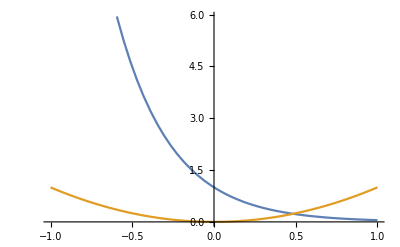

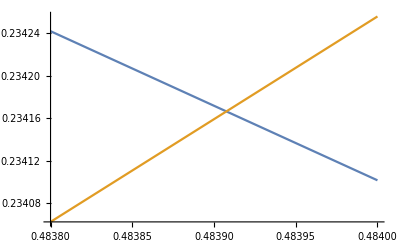

```mathematica
exp3a=E^(-3x);
exp3b=x^2;
plot4a= Plot[{exp3a,exp3b},{x,-1,1}]
plot4b=Plot[{exp3a,exp3b},{x,0.4838,0.4840},PlotRange->Automatic]
```

#### Point of Intersection:

Value of root obtained from the graph: 0.48391 UnderBar[+]0.0001

## Question 4:

4. Use Mathematica to explore an equation (or system of equations) that you have met in another lecture course. Start by explaining very briefly what the equations are describing in a short paragraph of text, being careful to explain the meaning of all symbols used in the equation(s).

Explore the equations using the techniques you have met so far in this course. You should explore the equation(s) graphically as well as symbolically. Consider using Animate, Manipulate, plotting, differentiation, integration, Solve, DSolve, FindRoot etc.

Explain briefly what your exploration with Mathematica has revealed to you about the equations. 

20 marks are available for this question so the number of marks awarded for your answer will depend partly on the complexity of the equation(s) explored. Exploring, F=ma, for example, will not reward you many marks.  However, the purpose of this question is to use Mathematica to discover something you may not have known without its use. [20 marks].

#### Setting up Damped Driven Simple Harmonic Oscillators equation of motion w/ Boundary conditions :

```mathematica
harm=m *D[x[t],{t,2}]+b *D[x[t],t]+k*x[t]== F0*Cos[w*t]
boundc1=x[0]==0
boundc2= x'[0]==0
```

k x[t]+b x'[t]+m x''[t]==F0 Cos[t w]

x[0]==0

x'[0]==0

I have chosen to explore the equation of motion of a damped driven SHM system; simple harmonic oscillators are systems in which a periodic motion is  drive by a resultant, restoratory force proportional to the displacement of the system from an equilibrium position and therefore the acceleration is always directed towards the equilibrium. When freely oscillating a SHM system oscillates at its natural frequency, however, under forced oscillations the systems motion depends on the driving frequency. If driven frequency is equal to the natural frequency resonance is observed and the amplitude of the oscillation experiences a maximal fortification. If a system is dampened a frictional force will produce a force opposing the oscillation resulting in the energy of the system being dissipated. Damping of a system can thus be used to reduce amplitude of a resonant oscillator and reduce the effects of resonance.  

In a SHM system we have a resultant force equal to the product of the inertia and the acceleration; a restorative torsional forces proportional to the displacement; a damping force proportional to velocity; and a sinusoidal periodic driving force as a product of the maximum driving torque and cosine of frequency. The equation of motion is thus given as;      m(ⅆ^2 x)/(ⅆ t^2)+bⅆx/ⅆt+ kx= F_0cos(wt),
where m= Mass of the oscillator; b= Dampening Constant; k= Stiffness Constant; F_0=Driven Amplitude; w= Driven Frequency. This is a second order differential, in a real system we would take the boundary conditions where at time, t=0, the displacement, x, is zero, and in addition, velocity ⅆx/ⅆt=0.

#### Solving for General and Specific solution:

```mathematica
harmsolve=DSolve[harm, x[t],t]
```

{{x[t]→ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) C[1]+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) C[2]-(4 F0 m^2 (k Cos[t w]-m w^2 Cos[t w]+b w Sin[t w]))/((-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))}}

```mathematica
harmsolvebound= DSolve[{harm, boundc1, boundc2}, x[t],t]
```

{{x[t]→-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2)))}}

We can use DSolve to get our general solution, we see the general solution depends on the discriminate of the roots of the analogous linear equation. Solving we get a complex general solution in which the real parts account for a real system; looking at the solve with boundary conditions, we get a linear sum of real sinusoidal expressions.

#### Plots for Specific Initial Values :

```mathematica
replace={m->10,b->.8,k->3,F0->19,w->6,C[1]-> 1,C[2]-> 1}
```

{m→10,b→0.8,k→3,F0→19,w→6,C[1]→1,C[2]→1}

Created a rule to replace the constant for specific values to plot a graph

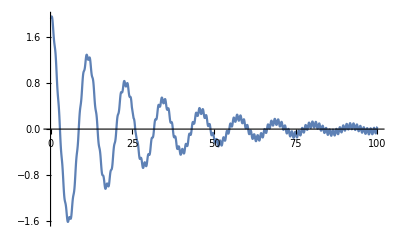

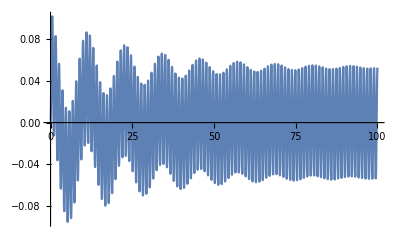

```mathematica
Plot[x[t]/.harmsolve/.replace,{t,0,100 }, PlotRange->Full]
Plot[x[t]/.harmsolvebound/.replace,{t,0,100 }, PlotRange->Full]
```

Plotting the these specific cases we see we get the expected sinusoidal pattern with the amplitude modulated over a exponential decay; however, unexpectedly, on the solution with no boundary conditions similar to a fourier series the sinusoidal function itself is a superposition of linear summation of different sine waves, ie. the function for the wave looks like a approximation made with a fourier transform. Moreover, the function with imposed boundary conditions looks similar to that of beats, in which a carrier wave is modulated by a envelop frequency wave. Subsequently, can explore this more with a interactive plot.

#### Interactive Plots:

Interactive plot for general solution, integration constant put to 1 and sliders allow you to change physical variables such as mass

```mathematica
Manipulate[Plot[3 ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t)+ 3 ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t)-(4 F0 m^2 (k Cos[t w]-m w^2 Cos[t w]+b w Sin[t w]))/((-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2)),{t,0,100}, PlotRange->Full],
{{m,1, "Mass, m"},1,20},
{{b,0, "Damping Constant, b"},0,2},
{{k,1,"Stiffnes Constant, k"},1,20},
{{F0,0,"Driving Amplitude,F0"},0,20},
{{w,0,"Driving Frequency, w"},0,20}]
```

Below this interactive plot is for the equation with boundary conditions, from the snapshots taken from the manipulate function, we can further see how the solution to the SHM oscillator is as able to show beats and superposition creating novel patterns, as the linear combinations modulate the overall frequency. I previously thought u could only get simple sinusoidal plots or those modulated by exponential decay from such a system with dampening.

```mathematica
Manipulate[Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,100}, PlotRange->Full],
{{m,1, "Mass, m"},1,20},{{b,0, "Damping Constant, b"},0,2},{{k,1,"Stiffnes Constant, k"},1,20},{{F0,1,"Driving Amplitude,F0"},1,20},{{w,0,"Driving Frequency, w"},0,20}]
```

#### Below are interesting specific values which produced unexpected plots:

```mathematica
DynamicModule[{b=0.686,F0=4.34,k=3.7800000000000002,m=9.18,w=0.},Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,100},PlotRange->Full]]
```

```mathematica
DynamicModule[{b=0.25,F0=5.2,k=2.74,m=3.7,w=7.44},Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,100},PlotRange->Full]]
```

```mathematica
DynamicModule[{b=0.,F0=11.,k=2.74,m=1.,w=1.84},Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,100},PlotRange->Full]]
```

```mathematica
DynamicModule[{b=0.,F0=17.14,k=6.5600000000000005,m=1.,w=10.28},Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,100},PlotRange->Full]]
```

```mathematica
DynamicModule[{b=0.544,F0=17.14,k=4.1,m=7.6000000000000005,w=10.28},Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,10},PlotRange->Full]]
```

```mathematica
DynamicModule[{b=0.066,F0=17.14,k=4.1,m=7.6000000000000005,w=10.28},Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,100},PlotRange->Full]]
```

```mathematica
DynamicModule[{b=0,F0=14.44,k=13.58,m=1,w=11.32},Plot[-((2 F0 m^2 (b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k-ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) k √(b^2-4 k m)-ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) k √(b^2-4 k m)+b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m w^2-b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m w^2+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) m √(b^2-4 k m) w^2+2 k √(b^2-4 k m) Cos[t w]-2 m √(b^2-4 k m) w^2 Cos[t w]+2 b √(b^2-4 k m) w Sin[t w]))/(√(b^2-4 k m) (-b^2+2 k m+b √(b^2-4 k m)-2 m^2 w^2) (b^2-2 k m+b √(b^2-4 k m)+2 m^2 w^2))),{t,0,100},PlotRange->Full]]
```

Total marks available: 46

Solutions are due by 4pm on Monday February 17th.
Make a copy of your solutions with the output deleted (Cell|Delete All Output) and upload that file to Moodle.
Please name the file to include your family name and first name, for example I would use hw1_Jasvir_Bhamrah.

The first thing I shall do when I get the file is to click Evaluation|Evaluate Notebook, so make sure the file you send me will survive that.

A.H. Harker, J Underwood, L McKemmish, J. Bhamrah
UCL
February 2016, February 2017, February 2018, February 2020